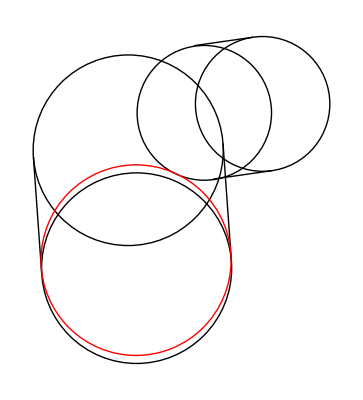

```mathematica
s12={7.59375,6.5};
s13={7.53125,7.375};
param=0.0680117675702504;
Graphics[{capsule[{8.09375,7.65625},{8.53125,7.71875},0.5],capsule[s12,s13,0.7071067811865476],Red,Circle[s12+param(s13-s12),0.7071067811865476]}]
```

```mathematica
quadProject[quad_,axis_]:=Module[{a,b,c,d},
a=Dot[axis,quad[[1]]];
b=Dot[axis,quad[[2]]];
c=Dot[axis,quad[[3]]];
d=Dot[axis,quad[[4]]];
{Min[a,b,c,d],Max[a,b,c,d]}
]
circleProject[circle_,axis_]:=Module[{a},
a=Dot[axis,circle[[1]]];
{a-circle[[2]],a+circle[[2]]}
]
point[a_,b_,param_]:=a+param(b-a)
quad={
{8.164460678118655,7.161275253169417},
{8.601960678118655,7.223775253169417},
{8.460539321881345,8.213724746830584},
{8.023039321881345,8.151224746830584}
};
circle=Circle[{7.59375,6.5},0.7071067811865476];
closest=quad[[1]];
```

```mathematica
Manipulate[
axis=Normalize[p];
qp=quadProject[quad,axis];
cp=circleProject[circle,axis];
Graphics[{Blue,Polygon[quad],Red,circle,Thickness[0.01],Black,Line[{{0,0},axis}],Blue,Line[{point[{0,0},axis,qp[[1]]],point[{0,0},axis,qp[[2]]]}],Red,Line[{point[{0,0},axis,cp[[1]]],point[{0,0},axis,cp[[2]]]}]},PlotRange->{{-5,10},{-5,10}}],{{p,{1,1}},Locator}]
```

```mathematica
n01={0.14142135623730945,-0.9899494936611666};
n12={0.9899494936611666,0.14142135623730914};
n23={-0.14142135623730953,0.9899494936611666};
n30={-0.9899494936611666,-0.14142135623730928};
a={-0.7570442108397464,0.6533636528259171};
```

{0.653364,0.757044}

{10.7558,11.746}

{9.17516,10.5894}

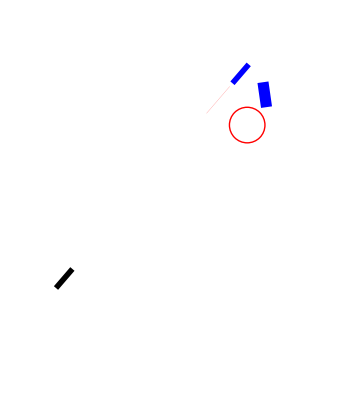

```mathematica
axis=Normalize[closest-circle[[1]]]
qp=quadProject[quad,axis]
cp=circleProject[circle,axis]
Graphics[{Blue,Polygon[quad],Red,circle,

Black,Thickness[0.01],Line[{{0,0},axis}],

Thickness[0.01],
Blue,Line[{point[{0,0},axis,qp[[1]]],point[{0,0},axis,qp[[2]]]}],

Thickness[0.0],
Red,Line[{point[{0,0},axis,cp[[1]]],point[{0,0},axis,cp[[2]]]}],

Null

},PlotRange->{{-1,10},{-3,10}}]
```